## forced van der Pol oscillator (Problem 11.21)

```mathematica
Clear["Global`*"];
```

```mathematica
vdP[ωext_,f0_,tend_]:=Module[{eq,init,ϵ,ω,x1,x2,t,x1sol,x2sol},
eq={x1'[t]==x2[t],x2'[t]==ϵ (1-x1[t]^2)x2[t]-x1[t]+f Cos[ω t]};
init={x1[0]==1,x2[0]==0};
{x1sol,x2sol}=NDSolveValue[{eq,init}/.{ϵ->0.1,f->f0,ω->ωext},{x1,x2},{t,0,tend}]]
(* ParametricPlot[{x1sol[t],x2sol[t]},{t,0,tend},PlotRange->All] *)
(* Plot[{x1sol[t],Cos[ω t]/.ω->1.1},{t,0,tend},PlotRange->All] *)
```

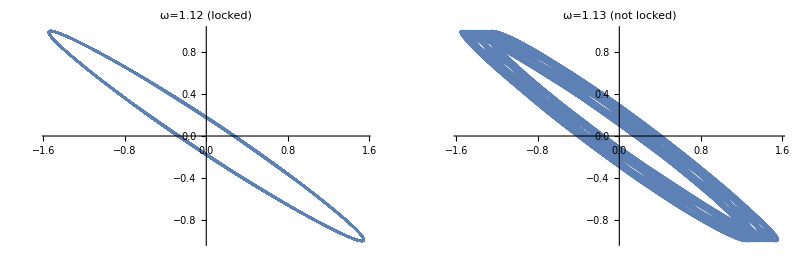

```mathematica
tend=2000;f=0.4;ω=1.12;
{x1s,x1sdot}=vdP[ω,f,tend];
p1=ParametricPlot[{x1s[t],Cos[ω t]},{t,tend-200,tend},PlotRange->All,PlotLabel->"ω=1.12 (locked)"];

ω=1.13;
{x2s,x2sdot}=vdP[ω,f,tend];
p2=ParametricPlot[{x2s[t],Cos[ω t]},{t,tend-200,tend},PlotRange->All,PlotLabel->"ω=1.13 (not locked)"];

GraphicsRow[{p1,p2}]
```